# 3 Bodies Spring

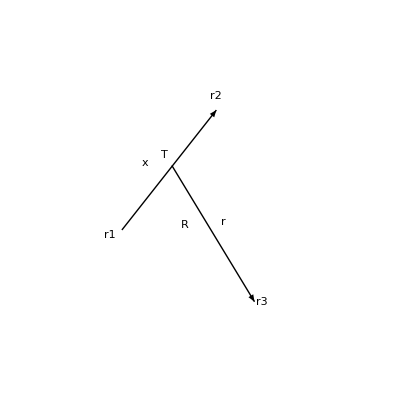

```mathematica
Solve[{m1 r1 + m2 r2 == (m1+m2) T,
x == r2 - r1},{r1,r2}]//FullSimplify
```

{{r1→T-(m2 x)/(m1+m2),r2→T+(m1 x)/(m1+m2)}}

```mathematica
r1== T-(m2 x)/m
r2== T+(m1 x)/m
```

```mathematica
Solve[{(m1+m2)T+ m3 r3 == (m1+m2+m3)R,
r == r3 - T},{T,r3}]//FullSimplify
```

{{T→-(m3 r)/(m1+m2+m3)+R,r3→((m1+m2) r)/(m1+m2+m3)+R}}

```mathematica
T==-(m3 r)/M+R
r3==(m r)/M+R
r1== -(m3 r)/M+R-(m2 x)/m
r2== -(m3 r)/M+R+(m1 x)/m
```

```mathematica
(* equation of motion *)
m1 D[r1[t],{t,2}] == k m1 m2 (r2-r1)+ k m1 m3 (r3-r1)
m2 D[r2[t],{t,2}] == k m1 m2( r1-r2)+ k m3 m2 (r3-r2)
m3 D[r3[t],{t,2}] == k m1 m3 (r1-r3)+ k m2 m3 (r2-r3)
```

```mathematica
(* Cyclic = periodic *)
```

```mathematica
m1 D[r1[t],{t,2}] == k m1 m2 (r2-r1)+ k m1 m3 (r3-r1)/.{r3-> (m r)/M,r1-> -(m3 r)/M-(m2 x)/m,r2->  -(m3 r)/M+(m1 x)/m}//FullSimplify
m2 D[r2[t],{t,2}] == k m1 m2 (r1-r2)+ k m3 m2 (r3-r2)/.{r3-> (m r)/M,r1-> -(m3 r)/M-(m2 x)/m,r2->  -(m3 r)/M+(m1 x)/m}//FullSimplify
m3 D[r3[t],{t,2}] == k m1 m3 (r1-r3)+ k m2 m3 (r2-r3)/.{r3-> (m r)/M,r1-> -(m3 r)/M-(m2 x)/m,r2->  -(m3 r)/M+(m1 x)/m}//FullSimplify
```

m1 (-(m3 r)/M-(m2 x)/m)''[t]==k m1 ((m3 (m+m3) r)/M+(m2 (m1+m2+m3) x)/m)

m2 (-(m3 r)/M+(m1 x)/m)''[t]==k m2 ((m3 (m+m3) r)/M-(m1 (m1+m2+m3) x)/m)

m3 ((k (m1+m2) (m+m3) r)/M+((m r)/M)''[t])==0

```mathematica
(-(m3 r)/M-(m2 x)/m)''[t]==k  ((m3 (m+m3) r)/M+(m2 M x)/m)
```

```mathematica
(-(m3 r)/M+(m1 x)/m)''[t]==k  ((m3 (m+m3) r)/M-(m1 M x)/m)
```

```mathematica
k ((m1+m2) (m+m3))/m r+r''[t]==0
```

```mathematica
DSolve[α^2 r[t]+r''[t]==0,r[t],t] (* α^2= k ((m1+m2) (m+m3))/m *)
```

{{r[t]→C[1] Cos[t α]+C[2] Sin[t α]}}

```mathematica
(* from 2 - 1 *)
DSolve[ x''[t]==-β^2 x[t],x[t],t] (* β^2= k M *)
```

{{x[t]→C[1] Cos[t β]+C[2] Sin[t β]}}

```mathematica
(* since they are vector *)
rx[t] == RxC Cos[ α t] + RxS Sin[α t]
ry[t] == RyC Cos[ α t] + RyS Sin[α t]
xx[t] == xxC Cos[ α t] + xxS Sin[α t]
xy[t]== xyC Cos[ α t] + xyS Sin[α t]
```